```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/SLattice/math"];
```

```mathematica
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)//Simplify
```

(m^2 x^4)/(96 π^2)

```mathematica
(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}//N
```

5.34311×10^-9

```mathematica
Sqrt[4 53+2]//N
```

14.6287

```mathematica
dNdata=Import["chaotic_dN.dat"]//Flatten;
```

```mathematica
dNmap=Flatten[Table[{x,y,z,dNdata[[17^2(z+8)+17(y+8)+(x+9)]]},{x,-8,8},{y,-8,8},{z,-8,8}],2];
```

```mathematica
ListDensityPlot3D[dNmap]
```

-Graphics3D-

```mathematica
L=17;
```

```mathematica
dNk[kx_,ky_,kz_]=1/L^(3/2)Sum[xx=dNmap[[i,1]];
yy=dNmap[[i,2]];
zz=dNmap[[i,3]];
dNmap[[i,4]]Exp[-I 2π(kx xx+ky yy+kz zz)/L],{i,Length[dNmap]}];
```

```mathematica
Abs[dNk[1,2,3]]^2
```

1.48762×10^-9

```mathematica
kmax=L-1;
c=0.05;
```

```mathematica
Pkdata[k_]:=Select[Flatten[Table[If[(*(k-(c k)/2)^2*)k^2<=kx^2+ky^2+kz^2<(*(k+(c k)/2)^2*)(k+c k)^2,Abs[dNk[kx,ky,kz]]^2,None],{kx,-0,kmax},{ky,0,kmax},{kz,0,kmax}],2],Positive]
```

```mathematica
PkList=Select[ParallelTable[Pkdatas=Pkdata[E^lnk];If[Length[Pkdatas]>1,{E^lnk,Total[Pkdatas]/(c L^3)±(Sqrt[Length[Pkdatas]]StandardDeviation[Pkdatas])/(c L^3)},None],{lnk,0,Log[Sqrt[3]kmax],c}],Length[#]>1&];//AbsoluteTiming
```

{28.6764,Null}

```mathematica
Total[Pkdata[10]]/(c L^3)
```

2.35045×10^-9

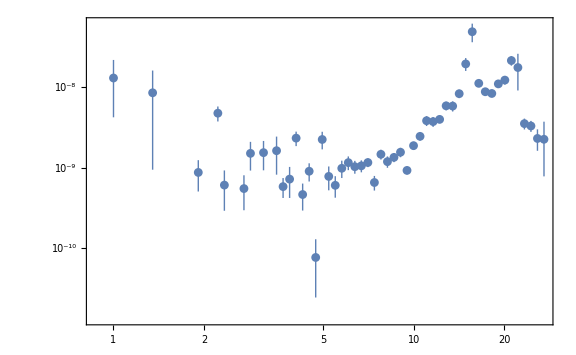

```mathematica
ListLogLogPlot[PkList,GridLines->{None,{(1/2 m^2 x^2)/(24 π^2 1/2((m^2 x)/(1/2 m^2 x^2))^2)/.{x->15,m->10^-5}}},Joined->False]
```

```mathematica
PkListWOe=Select[ParallelTable[Pkdatas=Pkdata[E^lnk];If[Length[Pkdatas]>1,Total[Pkdatas]/(c L^3),None],{lnk,0,Log[Sqrt[3]kmax],c}],Positive];//AbsoluteTiming
```

{29.0663,Null}

```mathematica
c Total[PkListWOe]
Variance[dNdata]
```

1.29302×10^-8

1.33038×10^-8